```mathematica
L:=1/2(m1 l1^2 ω1[t]^2+ m2 (l2^2 ω2[t]^2+l1^2 ω1[t]^2+2l1 l2 ω1[t]ω2[t] Cos[θ1[t]-θ2[t]]))+m1 g l1 Cos[θ1[t]] + m2 g (l2 Cos[θ2[t]]+l1 Cos[θ1[t]])
```

```mathematica
Lω1=D[L,ω1[t]]
```

1/2 (2 l1^2 m1 ω1[t]+m2 (2 l1^2 ω1[t]+2 l1 l2 Cos[θ1[t]-θ2[t]] ω2[t]))

```mathematica
Lθ1=D[L,θ1[t]]
```

-g l1 m1 Sin[θ1[t]]-g l1 m2 Sin[θ1[t]]-l1 l2 m2 Sin[θ1[t]-θ2[t]] ω1[t] ω2[t]

```mathematica
Lω2=D[L,ω2[t]]
```

1/2 m2 (2 l1 l2 Cos[θ1[t]-θ2[t]] ω1[t]+2 l2^2 ω2[t])

```mathematica
Lθ2=D[L,θ2[t]]
```

-g l2 m2 Sin[θ2[t]]+l1 l2 m2 Sin[θ1[t]-θ2[t]] ω1[t] ω2[t]

```mathematica
D[Lω2,t]
```

1/2 m2 (-2 l1 l2 Sin[θ1[t]-θ2[t]] ω1[t] (θ1'[t]-θ2'[t])+2 l1 l2 Cos[θ1[t]-θ2[t]] ω1'[t]+2 l2^2 ω2'[t])

```mathematica
Remove[a]
```

```mathematica
Manipulate[Module[{a=NDSolve[{θ1'[t]==ω1[t],θ2'[t]==ω2[t],D[Lω1,t]==Lθ1,D[Lω2,t]==Lθ2,θ1[0]==θ10,θ2[0]==θ20,ω1[0]==0,ω2[0]==0}/.{m1->mass1,m2->mass2,l1->length1,l2->length2,g->9.8},{θ1[t],ω1[t],θ2[t],ω2[t]},{t,-1,100}]},Show[ParametricPlot[{(Sin[θ1[t]]+Sin[θ2[t]]),-(Cos[θ1[t]]+Cos[θ2[t]])}/.a,{t,0,T},PlotRange->{{-2,2},{-2,1}}],ParametricPlot[{Sin[θ1[t]],-Cos[θ1[t]]}/.a,{t,0,T},PlotStyle->Red]]],{{mass1,1},0.1,10},{{mass2,1},0.1,10},{{length1,1},0.5,2},{{length2,1},0.5,2},{T,0.1,50},{{θ10,Pi/2},-2Pi/3,2Pi/3},{{θ20,0},-2Pi/3,2Pi/3}]
```

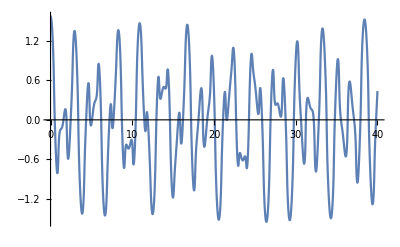

```mathematica
Plot[θ1[t]/.a,{t,0,40}]
```

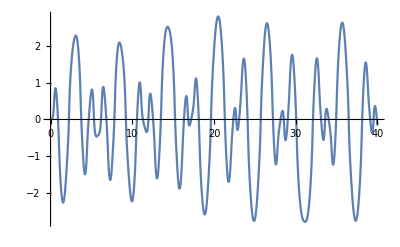

```mathematica
Plot[θ2[t]/.Out[7],{t,0,40}]
```

```mathematica
Animate[ContourPlot[-Cos[θ1[t]]y ==Sin[θ1[t]]x/.Out[7][[1,1]],{x,0,Cos[θ1[t]]},{y,0,Sin[θ1[t]]},PlotRange->{{-1,1},{-1,1}}],{t,0,5},AnimationRunning->False]
```

```mathematica
Plot[x[t]/.x[t]->t^2,{t,0,5}]
```

```mathematica
Sin[z[t]]x==Cos[z[t]]y/.z[t]->Sin[t]
```

x Sin[Sin[t]]==y Cos[Sin[t]]